# QCD calculation: 1-Loop Calculation

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
<<FeynArts`
<<FormCalc`
```

FeynArts 3.9

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 2 Dec 14

FormCalc 8.4

by Thomas Hahn

last revised 5 Nov 14

$CharacterEncoding::utf8: The byte sequence {160} could not be interpreted as a character in the UTF-8 character encoding.

### Create Topology

```mathematica
topo0=CreateTopologies[0,2->2];
topo1=CreateTopologies[1,2->2,ExcludeTopologies->{Internal}];
topologies=Join[topo1,topo0];
```

### q q' -> q q' with 1-loop diagram

loading generic model file /Users/misho/Documents/Mathematica/lib/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts/Models/SMQCD.mod

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 8 Classes, and 8 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 1 Classes insertion

> Top. 8: 0 Classes insertions

> Top. 9: 1 Classes insertion

> Top. 10: 0 Classes insertions

> Top. 11: 0 Classes insertions

> Top. 12: 0 Classes insertions

> Top. 13: 0 Classes insertions

> Top. 14: 0 Classes insertions

> Top. 15: 1 Classes insertion

> Top. 16: 0 Classes insertions

Restoring 0 Generic, 8 Classes, and 8 Particles fields

in total: 3 Classes insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

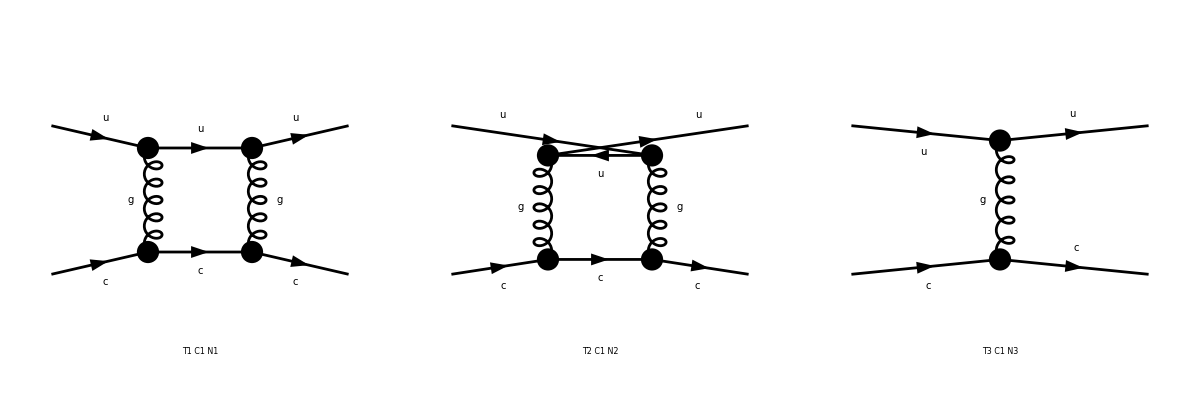

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

```mathematica
diag=InsertFields[topologies,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2],S[3]}];
Paint[diag];
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA];
```

Note that this process contains infrared divergence.

```mathematica
_Hel=0;
mat=4/9 SquaredME[amp]//.HelicityME[amp]//.ColourME[amp];
```

> 100 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

### Interpretation

```mathematica
VALUES={Den[p2_,m2_]:>1/(p2-m2),
Alfas->0.1,Alfas2->0.1^2,
MU->0.001,MU2->0.001^2,
MC->1.27,MC2->1.27^2};
MyResult=mat//.Subexpr[]//.Join[VALUES,{S->(2 200)^2,T->-0.4S, U->-S-T-2MU2-2MC2}]
```

4/9 (1)
 |  |  |  |

### Numerical Evaluation with LoopTools

```mathematica
Install["LoopTools"]
```

s::shdw: Symbol \!\("s"\) appears in multiple contexts \!\({"LoopTools`", "FormCalc`"}\); definitions in context \!\("LoopTools`"\) may shadow or be shadowed by other definitions.

LinkObject[…]

```mathematica
MyResult
```

ffxc0i: infra-red divergent threepoint function, working with a cutoff    1.0000000000000000     
 ffxdbd: using IR cutoff lambda^2 =    1.0000000000000000

3.16789+0. ⅈ

You saw IR divergence was detected. The result depends on the cut-off.

```mathematica
SetLambda[2.0]
MyResult
MyResult//Chop
```

7.61422-1.72701×10^-16 ⅈ

7.61422

# Tree Level v.s. 1-loop Level

We proceed, anyway, with ignoring the IR divergence. (i.e. the following calculation is physically invalid, but good as an example.)

```mathematica
Exit[];
```

```mathematica
$Language="English";
<<FeynArts`
<<FormCalc`
```

FeynArts 3.9

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 2 Dec 14

FormCalc 8.4

by Thomas Hahn

last revised 5 Nov 14

$CharacterEncoding::utf8: The byte sequence {160} could not be interpreted as a character in the UTF-8 character encoding.

### q q' -> q q' with tree level, cross terms, 1-loop level

```mathematica
topo0=CreateTopologies[0,2->2];
topo1=CreateTopologies[1,2->2,ExcludeTopologies->{Internal}];
```

loading generic model file /Users/misho/Documents/Mathematica/lib/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts/Models/SMQCD.mod

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 8 Classes, and 8 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 8 Classes, and 8 Particles fields

in total: 1 Classes insertion

Excluding 0 Generic, 8 Classes, and 8 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 1 Classes insertion

> Top. 8: 0 Classes insertions

> Top. 9: 1 Classes insertion

> Top. 10: 0 Classes insertions

> Top. 11: 0 Classes insertions

> Top. 12: 0 Classes insertions

Restoring 0 Generic, 8 Classes, and 8 Particles fields

in total: 2 Classes insertions

> Top. 1: 1 diagram

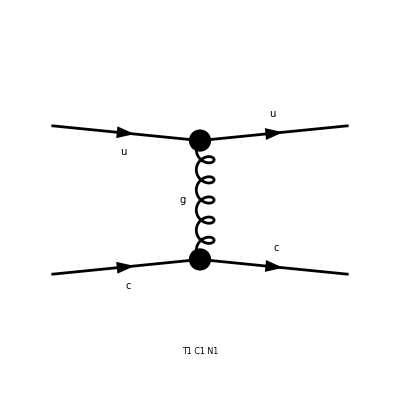

> Top. 1: 1 diagram

> Top. 2: 1 diagram

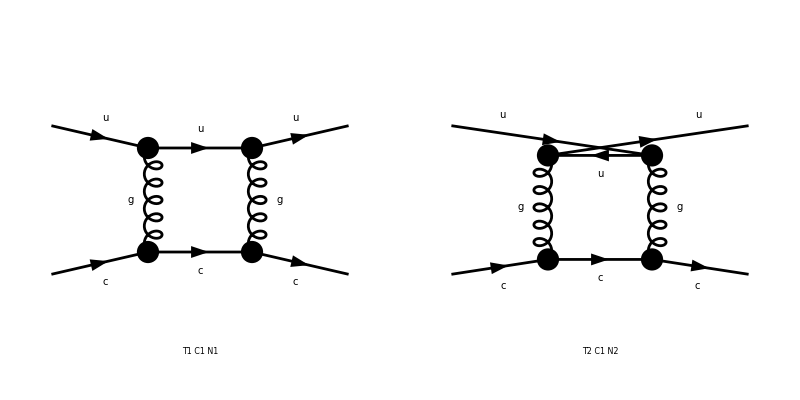

```mathematica
diag0=InsertFields[topo0,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2],S[3]}];
diag1=InsertFields[topo1,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2],S[3]}];
Paint[diag0];
Paint[diag1];
```

```mathematica
ClearProcess[];
amp0=CalcFeynAmp[CreateFeynAmp[diag0],FermionChains->VA];
amp1=CalcFeynAmp[CreateFeynAmp[diag1],FermionChains->VA];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM... running FORM...

ok

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

in total: 2 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-1.frm

ok

```mathematica
_Hel=0;
tree=4/9 SquaredME[amp0]//.HelicityME[amp0]//.ColourME[amp0];
cross=4/9 SquaredME[amp1,amp0]//.HelicityME[amp1,amp0]//.ColourME[amp1,amp0];
loop=4/9 SquaredME[amp1]//.HelicityME[amp1]//.ColourME[amp1];
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM... running FORM... running FORM...

ok

> 40 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

ok

> 100 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

ok

### Numerical Evaluation

```mathematica
Install["LoopTools"]

VALUES={Den[p2_,m2_]:>1/(p2-m2),
Alfas->0.1,Alfas2->0.1^2,
MU->0.001,MU2->0.001^2,
MC->1.27,MC2->1.27^2};
Ntree=tree//.Subexpr[]//.Join[VALUES,{S->(2 200)^2,T->-0.4S, U->-S-T-2MU2-2MC2}]
Ncross=cross//.Subexpr[]//.Join[VALUES,{S->(2 200)^2,T->-0.4S, U->-S-T-2MU2-2MC2}]
Nloop=loop//.Subexpr[]//.Join[VALUES,{S->(2 200)^2,T->-0.4S, U->-S-T-2MU2-2MC2}]
```

s::shdw: Symbol \!\("s"\) appears in multiple contexts \!\({"LoopTools`", "FormCalc`"}\); definitions in context \!\("LoopTools`"\) may shadow or be shadowed by other definitions.

LinkObject[…]

5.96573

ffxc0i: infra-red divergent threepoint function, working with a cutoff    1.0000000000000000     
 ffxdbd: using IR cutoff lambda^2 =    1.0000000000000000

-3.84273+2.17541 ⅈ

4.88761-1.97373×10^-16 ⅈ

```mathematica
{treeLevel,loopLevel}={Ntree,Ntree+2Re[Ncross]+Nloop}
```

{5.96573,3.16789-1.97373×10^-16 ⅈ}

We can see that the infrared divergences are not cured well.

```mathematica
VAL[mass_]:={Den[p2_,m2_]:>1/(p2-m2),Alfas->0.1,Alfas2->0.1^2,MU->mass,MU2->mass^2,MC->1.27,MC2->1.27^2};
loop//.Subexpr[]//.Join[VAL[0.00001],{S->(2 200)^2,T->-0.4S, U->-S-T-2MU2-2MC2}]
loop//.Subexpr[]//.Join[VAL[0.0001],{S->(2 200)^2,T->-0.4S, U->-S-T-2MU2-2MC2}]
loop//.Subexpr[]//.Join[VAL[0.001],{S->(2 200)^2,T->-0.4S, U->-S-T-2MU2-2MC2}]
loop//.Subexpr[]//.Join[VAL[0.01],{S->(2 200)^2,T->-0.4S, U->-S-T-2MU2-2MC2}]
loop//.Subexpr[]//.Join[VAL[0.1],{S->(2 200)^2,T->-0.4S, U->-S-T-2MU2-2MC2}]
```

71.6298-5.92119×10^-16 ⅈ

10.0018+4.93432×10^-17 ⅈ

4.88761-1.97373×10^-16 ⅈ

24.1733+9.86865×10^-17 ⅈ

44.9204+0. ⅈ